{35.4,40.2,80.1,25.2}

{15,15,11,13}

{1.18,1.34,3.64091,0.969231}

23.7671 % athlete profit

90.45 $ Nceno profit

3.015 Nceno ROI of stake $ Nceno profit

3.76875 % of user stake per user per week $ Nceno profit

4.5225 rev per user $ Nceno profit

1.13063 rev per user per week $ Nceno profit

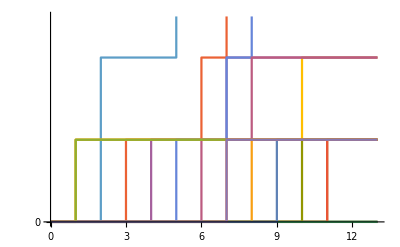

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
failRate = 0.1; (*failure rate*)
weeks = 4; (*in weeks*)
ses =3; (*days per week quota*)
ppl = 20;
lim =3; 
perc={{100,0,0,0,0,0,0,0,0,0,0,0},{32,68,0,0,0,0,0,0,0,0,0,0},{17,33,50,0,0,0,0,0,0,0,0,0},{12,20,35,33,0,0,0,0,0,0,0,0},{9,17,20,24,30,0,0,0,0,0,0,0},{9,9,15,18,22,27,0,0,0,0,0,0},{8,8,14,13,18,17,22,0,0,0,0,0},{8,5,9,11,15,20,15,17,0,0,0,0},{6,4,7,13,9,11,19,17,14,0,0,0},{5,3,7,10,7,13,11,13,19,12,0,0},{5,3,6,6,11,6,10,16,7,19,11,0},{4,3,5,5,11,4,12,6,17,5,18,10}};
cost = 10;

workout = Range[0,ses weeks,1];
misses= Range[0,ppl ses weeks,1];
players = RandomFunction[PoissonProcess[ failRate],{0,weeks ses,1},ppl];
data = Normal[players];
fails = Table[data[[All,(s+1),2]]-data[[All,(s),2]],{s,1,ses weeks}] ;(*fails is a set of workouts. Each workout is an array. Each index is a player. Each player is a failure count.*)
 
pot = Table[0,weeks];
(*table of lost stake by week... needs careful attention*)

strikes = Table[0,ppl];

winners =Table[0,weeks]; (*weekly winner count*)

For[p=1,p<ppl+1,p++,
For[w=1,w<weeks+1,w++,
If[strikes[[p]]<lim,
prevStrikes=strikes[[p]];
failSum=0;
For[x=(w-1)*ses+1,x<w*ses+1,x++,
failSum+=fails[[x,p]];
] ;
If[failSum==0,winners[[w]]++,
strikes[[p]]+=failSum;
For[f=prevStrikes+1,f<strikes[[p]]+1,f++,
pot[[w]]+=0.01*perc[[lim,f]]*cost*lim;
]
];
]
];
]

pot
winners
payouts = Table[0,weeks]; 
For[w=1,w<weeks+1,w++,
If[winners[[w]]>0,payouts[[w]]= 0.5*pot[[w]]/winners[[w]],
payouts[[w]]=0]
]

payouts 

100*(Sum[payouts[[i]],{i,1,weeks}]/(lim*cost))"% athlete profit"

ncenoPO = Table[0,weeks]; (*Nceno revenue*)
For[w=1,w<weeks+1,w++,
ncenoPO[[w]]= .5 pot[[w]]
]

ncenoProfit = Sum[ncenoPO[[i]],{i,1,weeks}] "$ Nceno profit"
ncenoMargin = ncenoProfit/(lim*cost) "Nceno ROI of stake"
100 ncenoProfit/(N[ppl*lim*cost*weeks]) "% of user stake per user per week"
ncenoProfit/(ppl) "rev per user"
ncenoProfit/(ppl*weeks) "rev per user per week"

ListStepPlot[players,Filling->None,Ticks->{workout,misses}, PlotRange->{{0,weeks ses+1},Automatic}]
fails;
MatrixForm[fails]
```